```mathematica
allGraphs4[K4Key,"parents"]
```

{363,361,355,337,283,121}

```mathematica
MobiusGraphDouble[key_,key2_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"],form2=allGraphs[key2,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
mob=MobiusGraph4[key2,allGraphs];
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[TableForm[{n,Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]},TableAlignments->Center],found[n,"graph"]],{Left}
],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding",
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->800]
]
```

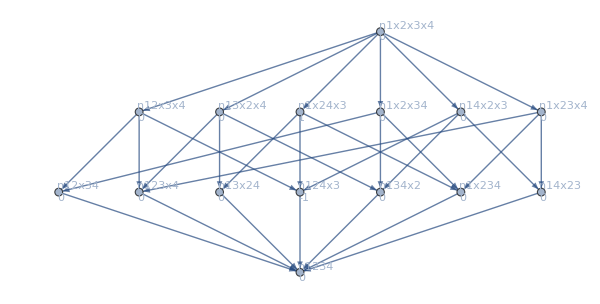
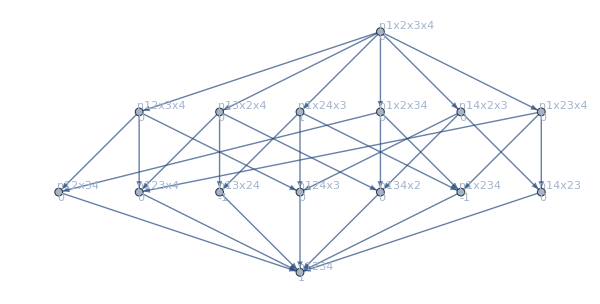
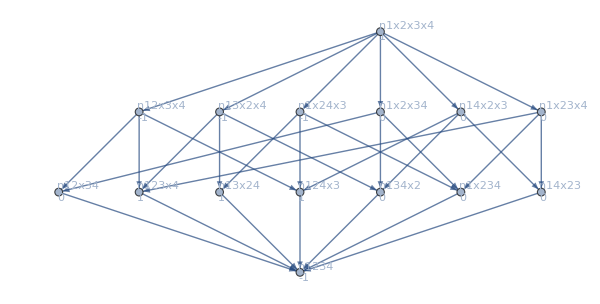
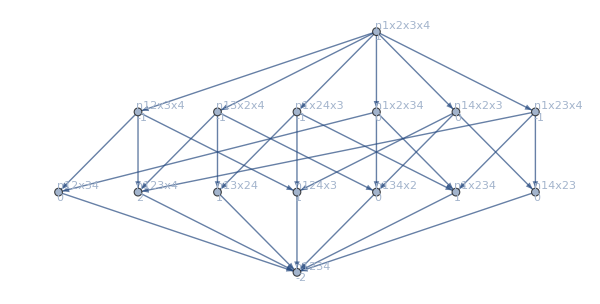
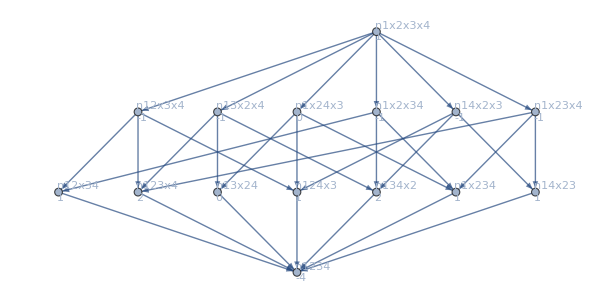
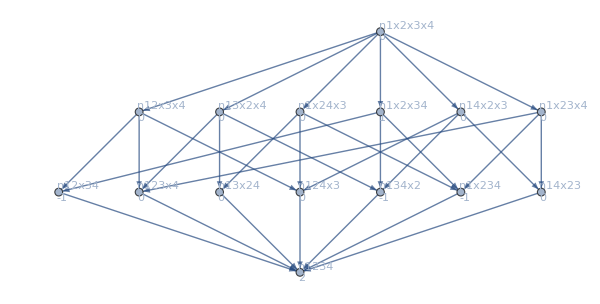
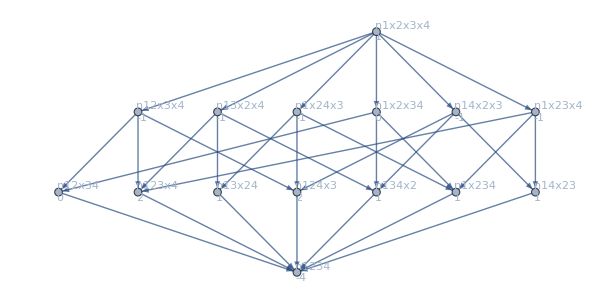
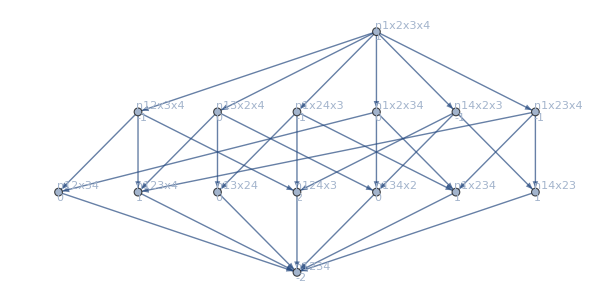
{-Graphics-276-Graphics--n124x3+n1x24x3{x^3-x^2,(x-1) x^2,18,-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-97-Graphics-n1234-n13x24-n1x234+n1x24x3{x^3-2 x^2+x,(x-1)^2 x,12,-Graphics-+-Graphics-}Null,-Graphics-327-Graphics--n1234+n123x4+n124x3-n12x3x4+n13x24-n13x2x4-n1x24x3+n1x2x3x4{x^4-3 x^3+3 x^2-x,(x-1)^3 x,24,-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-336-Graphics--2 n1234+2 n123x4+n124x3-n12x3x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4{x^4-4 x^3+5 x^2-2 x,(x-2) (x-1)^2 x,12,-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-361-Graphics--4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4{x^4-5 x^3+8 x^2-4 x,(x-2)^2 (x-1) x,6,-Graphics-+-Graphics-}Null,-Graphics-365-Graphics-2 n1234-n12x34-n134x2-n1x234+n1x2x34{x^3-3 x^2+2 x,(x-2) (x-1) x,6,-Graphics-}Null,-Graphics-363-Graphics--4 n1234+2 n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4{x^4-5 x^3+8 x^2-4 x,(x-2)^2 (x-1) x,6,-Graphics-+-Graphics-}Null,-Graphics-282-Graphics--2 n1234+n123x4+2 n124x3-n12x3x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4{x^4-4 x^3+5 x^2-2 x,(x-2) (x-1)^2 x,12,-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-346-Graphics-n1234-n123x4-n1x234+n1x23x4{x^3-2 x^2+x,(x-1)^2 x,12,-Graphics-+-Graphics-}Null,-Graphics-26-Graphics-n1x234{x^2,x^2,9,-Graphics-+-Graphics-}Null,-Graphics-488-Graphics-n12x34{x^2,x^2,9,-Graphics-+-Graphics-}Null,-Graphics-18-Graphics-n1x23x4{x^3,x^3,27,-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-728-Graphics-n1234{x,x,3,-Graphics-}Null,-Graphics-1-Graphics--n1x2x34+n1x2x3x4{x^4-x^3,(x-1) x^3,54,-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-354-Graphics--2 n1234+n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4{x^4-4 x^3+5 x^2-2 x,(x-2) (x-1)^2 x,12,-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-111-Graphics--n1234+n124x3+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4{x^4-3 x^3+3 x^2-x,(x-1)^3 x,24,-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-417-Graphics-n1234-n123x4-n13x24+n13x2x4{x^3-2 x^2+x,(x-1)^2 x,12,-Graphics-+-Graphics-}Null,-Graphics-280-Graphics--3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4{x^4-4 x^3+6 x^2-3 x,(x-1) x (x^2-3 x+3),18,-Graphics-+-Graphics-+-Graphics-+-Graphics-}Null,-Graphics-72-Graphics-n14x23{x^2,x^2,9,-Graphics-+-Graphics-}Null,-Graphics-355-Graphics--4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4{x^4-5 x^3+8 x^2-4 x,(x-2)^2 (x-1) x,6,-Graphics-+-Graphics-}Null}

```mathematica
Table[
With[
{g=MobiusGraphDouble[K4Key,k,allGraphs4], gr=allGraphs4[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
g
}],
{Style[StandardForm[allGraphs4[k,"colofourrealnull"]],Darker[Green],8],
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Style[ChromaticPolynomial[gr,3],Blue],
Style[StandardForm[allGraphs4[k,"colofour"]/.repBase4],Darker[Green],8]},
},
{Top,Bottom,Bottom}
]
]
]
,{k,RandomSample[ Keys[allGraphs4],20]}
]
```